# Welcome to Mathematica.

## Tutorial 1: Getting Started

Overview of Mathematica’s capabilities

Introduction to Notebooks

Practicing getting help

Exploring the documentation center

Click on the forward arrow below to continue.


This tutorial is based on and uses materials from Wolfram Mathematica 7's "Learn with guided examples"

◀     |     ▶

## Using Mathematica as a calculator

You can use Mathematica as a calculator.

Move your cursor below this text until it becomes a horizontal cursor.  Then click.

Next, type in 2+2.

Then press Shift-Return  (Hold down Shift and press Return).

◀     |     ▶

## Using Mathematica as a calculator

Try it again with something more complicated like 500! or 78^3.  Remember: To calculate an expression, you must use Shift-Return.

You can modify anything you type and re-evaluate.  Do this now to see how your calculation changes.

◀     |     ▶

## Making and modifying a plot

When you have existing input/output cells it's easy to go back and edit them, just as you would in a word processor.
Try changing Cos[3 x] to Cos[5 x] in the Plot command below, then press  to reevaluate the input. The new output will replace the old.

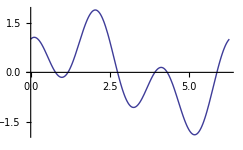

```mathematica
Plot[Sin[x]+Cos[3 x],{x,0,2Pi}]
```

Try making some changes to the input on this page before moving to the next page.

◀     |     ▶

## Captial Letters and Square Brackets

Now that you've learned how to get around in Mathematica, we'll start looking at the Mathematica language in more detail.
The most basic rule to know is that all built-in Mathematica functions start with capital letters and enclose their arguments in square brackets.
Click in each of these input cells and press  to see the result.

```mathematica
Plot[BesselJ[1,x],{x,0,30}]
```

Multiword function names use internal capitalization.

```mathematica
ListPlot[Table[Prime[n],{n,1,30}]]
```

Even standard math functions like sin and cos start with a capital letter.

```mathematica
Cos[0]
```

The constants e, i, and π also use capital letters.

```mathematica
N[{E,I,Pi}]
```

Because of this strict rule, you are free to use any name that starts with a lowercase letter for your own purposes. For example, you can use lowercase i as an index variable.

```mathematica
Table[i,{i,1,10}]
```

◀     |     ▶

## Lists

Curly brackets are used to hold lists of expressions separated by commas: anything can be made into a list.
When you evaluate a list, each of the elements in the list is evaluated and the results returned in another list.
Evaluate the examples below and you'll see how this works.

```mathematica
{1,2,3,x, y,z}
```

```mathematica
{Integrate[x^2, x],Integrate[Sin[x],x],Integrate[Tan[x],x]}
```

Lists really can hold anything, including 2D or 3D graphics.

```mathematica
{Plot[Sin[x],{x,0,2Pi}],Plot[Sin[2x],{x,0,2Pi}],Plot[Sin[3x],{x,0,2Pi}],Plot[Sin[4x],{x,0,2Pi}]}
```

Evaluate this example to see three interesting knots in a list.

```mathematica
{KnotData["Trefoil"],KnotData["FigureEight"],KnotData["Stevedore"]}
```

Click and drag the individual knots to see them from any angle.

◀     |     ▶

## Returning and Manipulating Lists

Many commands return lists as their result. For example, the list of plots from the previous page can be created more efficiently using the Table command.

```mathematica
Table[Plot[Sin[n x],{x,0,2Pi}],{n,1,4}]
```

Many functions allow you to create, operate on, or restructure lists. Here are just a few.

```mathematica
Sort[{3,1,2,5,4}]
```

```mathematica
Reverse[{1,2,3,4,5}]
```

```mathematica
Permutations[{1,2,3}]
```

To see the full range of functions for dealing with lists, see the guide page for List Manipulation (which will open in a separate window).

◀     |     ▶

## Range Specifications

One important use of lists is to hold range specifications (also commonly known as iterators).
Each of the commands below contains a set of three elements enclosed in curly brackets.
	{variable,min,max}  
Evaluate each of the inputs on this page. Some of them are quite fun!

```mathematica
Table[i,{i,1,10}]
```

```mathematica
Plot[Sin[x],{x,0,2Pi}]
```

```mathematica
Manipulate[Plot[Sin[n x],{x,0,2Pi}],{n,1,10}]
```

This iterator form is found in hundreds of Mathematica functions with slight variations in interpretation and allowed elements.
In many cases an optional fourth element specifies a step size.

```mathematica
Table[i^2,{i,0,10,2}]
```

A two-element form assumes a minimum of 1 and a step size of 1.

```mathematica
Table[i^2,{i,10}]
```

The iterator used in Plot requires exactly three elements. The effective step size is variable and is determined automatically in order to make a smooth curve.

```mathematica
Plot[Sin[x],{x,0,2Pi}]
```

In Manipulate a step size can be specified. If it is omitted, the variable is allowed to take on a continuous range of values.
This example allows n to take on a continuous range of real numbers.

```mathematica
Manipulate[Expand[(1+x)^n],{n,0,100}]
```

Here n is restricted to exact integers, allowing the Expand function to do its job.

```mathematica
Manipulate[Expand[(1+x)^n],{n,0,100,1}]
```

Manipulate in particular allows for a very wide range of such forms, extending well beyond the simple min-max range. See the full documentation on Manipulate (which will open in a separate window).

◀     |     ▶

## Options

Many Mathematica functions allow you to control their behavior using options, which are placed after any required or optional arguments in the function call.
For example, by default Plot gives you a set of axes.

```mathematica
Plot[Sin[x],{x,0,2Pi}]
```

If you want a box around the plot instead of axes, you can add the option Frame → True.

```mathematica
Plot[Sin[x],{x,0,2Pi},Frame->True]
```

Options always come at the end, and multiple options are separated by commas.

```mathematica
Plot[Sin[x],{x,0,2Pi},Frame->True,PlotStyle->Green]
```

You get the arrow character (→) by typing dash (-) followed by the greater-than sign (>). When you type the next character after the greater-than sign, the -> is automatically converted into →.
To find out what options a given function supports, you can look it up in the help system (the easiest way is to select the name of the function somewhere in your notebook, then press ).
Try it on the word Integrate below.

```mathematica
Integrate
```

Or if you already know what you're looking for and just need a reminder of the name, you can evaluate Options[function], for example.

```mathematica
Options[Integrate]
```

{Assumptions:>$Assumptions,GenerateConditions→Automatic,PrincipalValue→False}

◀     |     ▶

## Multiline Input and Suppressing Output

Single input expressions can be more than one line long: wordwrapping is automatic and intelligent, based on the nesting structure of the expression.

```mathematica
Plot[Sin[x],{x,0,2Pi},Frame->True,PlotStyle->Green,PlotLabel->"A plot of the sine function",ImageSize->200]
```

You can use the  key to add manual line breaks if you like.

```mathematica
Plot[Sin[x],{x,0,2Pi},
Frame->True,
PlotStyle->Green,
PlotLabel->"A plot of the sine function",
ImageSize->200]
```

You can also put more than one independent expression in the same input cell, using the  key to separate them.
Each line of syntactically complete input results in a separate output cell.
Try it now by evaluating the input cell below.

```mathematica
100!
Integrate[1/(1-x^3),x]
```

A semicolon can be used to suppress output.
When assigning a variable, for example, you may not want to see the value printed out.

```mathematica
a=10;
```

(Even after evaluation, this input cell is not followed by an output cell.)
It's common to use semicolons to suppress output from all but the last line in a multiline input cell.
Evaluate this input cell and note that you get only one output.

```mathematica
a=2;
b=-10;
c=12;
Solve[a x^2+b x+c==0,x]
```

When evaluating multiline inputs you can place the insertion point anywhere in the text of the input cell. When you press , the entire input cell will be evaluated regardless of where the insertion point was placed.
You can also click the cell bracket at the right edge of the window before pressing . If you select multiple cell brackets, all the selected input cells will be evaluated in order when you press .

◀     |     ▶

## Exact and Approximate Numbers

Mathematica distinguishes between exact integers and approximate real numbers. When given exact input, the system will not make approximations, even if it means nothing can be done with the input. For example, compare the output of these two commands.

```mathematica
Sqrt[2]
```

√2

```mathematica
Sqrt[2.]
```

1.41421

In the first case, the system has not computed the square root because there is no simpler way to represent the square root of two exactly, other than by saying it's the square root of two.
In the second case, the input included a decimal point, indicating that it was meant as an approximate real number. This caused Mathematica to give an approximate real-number result.
The command N can be used to request a numerical approximation to inputs given in exact form.

```mathematica
N[Sqrt[2]]
```

1.41421

An optional second argument can be used to specify the number of digits of precision you would like.

```mathematica
N[Sqrt[2],100]
```

1.414213562373095048801688724209698078569671875376948073176679737990732478462107038850387534327641573

There is no arbitrary limit to the number of digits in exact integer or floating-point numbers in Mathematica. Each of these examples gives a result with about half a million digits in it, and finishes in a couple of seconds on most computers. Try them now by clicking in and evaluating each of these input cells.

```mathematica
100000!
```

```mathematica
N[Pi,500000]
```

◀     |     ▶

## Equality versus Assignment

Mathematica distinguishes between equality testing and variable or function assignment.
Equality testing is done with ==, and the return value, if equality can be determined, is True or False.

```mathematica
1==2
```

False

```mathematica
1.0==1
```

True

Anywhere equations are used, == is the appropriate operator to use. For example, you can solve a simple algebraic equation.

```mathematica
Solve[x^2==9,x]
```

{{x→-3},{x→3}}

The more specialized === (three equal signs) operator tests for exact identity rather than mathematical equality.
For example, the equality of two variables cannot be established without knowing their values, so this example returns unevaluated unless x and y both have values assigned to them.

```mathematica
x==y
```

x==y

On the other hand, using === results in False because the two expressions are not literally identical.

```mathematica
x===y
```

False

Using === will always return True or False, while == may return True, False, or remain unevaluated.

◀     |     ▶

## Assignment

Simple variable assignment is done with the = operator. When this cell is evaluated, the symbol a is given the value 5.

```mathematica
a=5;
```

The value can then be used anywhere.  
Be sure to evaluate the cell above before trying these examples, otherwise the assignment won't have been made.

```mathematica
a^2
```

```mathematica
Plot[Sin[a x],{x,0,2Pi}]
```

Multiple assignments can be placed in a single cell. It is not necessary to select all the lines you want evaluated before pressing . An insertion point anywhere in the cell will do.

```mathematica
a=2;
b=4;
c=8;
```

Functions are defined using := instead of =. (The difference between = and := is explained in the tutorial "Immediate and Delayed Definitions".)
Here is a function that squares its argument.

```mathematica
f[x_]:=x^2
```

The _ (blank) character on the left-hand side is critical: it must appear after the argument name on the left but not on the right of the equal sign. The meaning of the blank is explained in the "Patterns" tutorial.
One of the powerful features of Mathematica is that once you have defined a function you can apply it to all kinds of input.
Be sure to evaluate the definition above before trying the examples below.
You can give it smple numbers.

```mathematica
f[5]
```

Or high-precision floating-point numbers or large integers.

```mathematica
f[N[Pi,100]]
```

```mathematica
f[100!]
```

Or symbolic quantities.

```mathematica
f[q+w]
```

You can plot your function using any of the built-in plotting functions.

```mathematica
Plot[f[x],{x,0,10}]
```

Because Mathematica processes functions symbolically, you can even integrate or differentiate the function, getting exact symbolic results.

```mathematica
Integrate[f[x],x]
```

```mathematica
D[f[x],x]
```

Further details on functions and patterns can be found in the tutorial "Defining Variables and Functions".

◀     |     ▶

## Automatic Syntax Coloring

Mathematica automatically colors symbols, brackets, and operators to indicate errors or likely errors. 
When you type a function name, it starts out blue and turns black when it matches the name of a built-in or user-defined symbol.

```mathematica
P
Pl
Plo
Plot
Plot3
Plot3D
```

A blue symbol is not necessarily an error; it simply means that the symbol does not currently have any value or definition associated with it. For example, before the following line is evaluated, the symbol name on the left-hand side is blue, but after evaluation it turns black because a value has been assigned to it. 
Try this now by evaluating the input cell.

```mathematica
value=7;
```

Unmatched brackets or parentheses are given a reddish purple color that indicates a syntax error.

```mathematica
Table[i,{i,1,10]
```

If you nevertheless evaluate such an input, emphasis is added to the unmatched elements in the form of a yellow background. Clicking the yellow -Graphics- symbol near the cell bracket will print out an error message describing the problem (but only after you have evaluated the input).

```mathematica
Table[i,{i,1,10]
```

When a function requires more arguments than you've given it, a red caret indicates where more are needed. Conversely, when a function has been given too many arguments, the excess arguments are colored red.

```mathematica
Integrate[x]
Sin[a,b]
```

Incorrect option names are colored red.

```mathematica
Plot[Sin[x],{x,0,2Pi},PlotArea->{-1,1}]
```

Local variables of several types are specially colored: in each case below, the variable x is colored (or italicized) because during evaluation it will be given a local value that overrides any global value that may be assigned to it.

```mathematica
func[x_]:=x^2
Module[{x},x+2]
Table[x,{x,0,10}]
```

The Preferences panel allows you to control these and other syntax coloring features, or turn them off.

◀     |     ▶

## Interactivity using Manipulate

Nearly any command can be made interactive by wrapping it in Manipulate. 
Be sure to evaluate the inputs below. This page won't make much sense if you don't.
The first argument to Manipulate is the function to be made interactive. The second and subsequent arguments specify parameters and ranges.

```mathematica
Manipulate[n!,{n,1,1000,1}]
```

You can specify multiple parameters by giving multiple range specifications.

```mathematica
Manipulate[Binomial[a,b],{a,1,1000,1},{b,1,1000,1}]
```

If the step size is omitted, the parameter is allowed to vary continuously.

```mathematica
Manipulate[Plot[Sin[n x],{x,0,2Pi}],{n,1,10}]
```

You can use a sublist in place of the range to give a parameter a discrete set of values.

```mathematica
Manipulate[Plot[Sin[n x],{x,0,2Pi},Filling->filling],
{n,1,10},
{filling,{None,Axis,Bottom,Top}}]
```

In order to ensure good interactive performance, many Mathematica plotting functions automatically simplify their results while sliders are being used, then generate a higher-quality result when the slider is released. Note how this plot looks jagged, but only while the slider is being dragged.

```mathematica
Manipulate[Plot3D[Sin[n x y],{x,0,3},{y,0,3}],{n,1,4}]
```

Complete details, including information about how to use Manipulate with slower functions, is available in the tutorial "Introduction to Manipulate".

◀     |     ▶

## Getting Help

The Documentation Center is the starting point for all help, including tutorials, guide pages, and function home pages. It's always available from the top of the Help menu.

The Function Navigator is a convenient way to find the function you need if you have a specific operation in mind. It's available from the Help menu or the Documentation Center.

The online Learning Center is a resource for finding tutorial videos.

If you already know or can guess the function you need, and just want to be reminded of its arguments, the ? operator is a quick way to get information without opening a new window.

```mathematica
?Integrate
```

Integrate[f,x] gives the indefinite integral ∫f dx. 
Integrate[f,{x,x_min,x_max}] gives the definite integral ∫_x_min^x_max f dx. 
Integrate[f,{x,x_min,x_max},{y,y_min,y_max},…] gives the multiple integral ∫_x_min^x_max dx∫_y_min^y_max dy … f.

The » at the end of the message is a link that takes you directly to the function's full reference page.
You can also select any word or function name and press  to open its function reference page.

◀     |     ▶

## Upward and Onward

Where to go from here?  Explore!  I suggest the following

Explore the Documentation Center.  (Click on Help > Documentation Center)
This is the best place to:

Learn how to use a function in Mathematica.

Get ready-to-go examples to practice with and build on.

Explore Mathematica's capabilities.

Especially explore the documentation on: Manipulate and Plot.

Visit the Demonstrations Project online.   (http://www.demonstrations.wolfram.com/)

See examples of Mathematica in action in many fields of science and mathematics.

Visit Wolfram Alpha to get started, and then download as "Live Mathematica" (bottom of output) to modify and edit in Mathematica.

◀     |     ▶